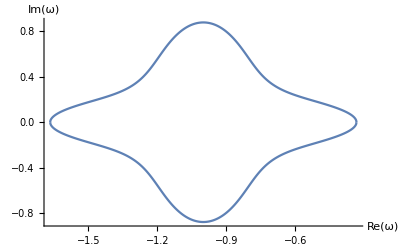

upper_example.csv

lower_example.csv

omx_example.csv

```mathematica
(*Produces the theoretical prediction for the boundary of the eigenvalue spectra in Fig. 2*)

Clear["Global`*"];
eff0 = 0.001;
(*Model parameters*)
(*Proportion of the population composed of prey and predator species respectively*)
gammafracu = 2.0/3.0;
gammafracv = 1.0/3.0;
(*Intraspecies interaction*)
du = 1.0;
dv = 1.0;
(*Interspecies interaction statistics*)
complexity =0.375;
f = 3.0;
ncmuuu =2.0 f;
ncmuuv = -2.0 f;
ncmuvu = 2.0 f;
ncmuvv = -1.0 f;
gammau = 0.5;
gammauv =-0.9;
gammav = -0.5;
(*Diffusion coefficients and wavenumber*)
ddu = 1.0;
ddv = 5.0;
q = 0.0;

(*Finding the boundary of the eigenvalue spectrum as a function of the real part of the eigenvalue: omx*)
(*Range over which to find the boundary and the number of points at which to sample*)
omminx = -1.8;
ommaxx = -0.2;
numomx = 1001;
omx = Table[om,{om,omminx ,ommaxx,(ommaxx -omminx)/(numomx -1)}];
lower= Table[0,{om,omminx ,ommaxx,(ommaxx -omminx)/(numomx -1)}];
upper= Table[0,{om,omminx ,ommaxx,(ommaxx -omminx)/(numomx -1)}];

Monitor[
For[i = 1, i<numomx +1, i++,
flagup = 0;
flagdown = 0;
flagdoneup = 0;
flagdonedown = 0;
(*solving the simulataneous equations in Eq. (S81) for omy (the complex part of the eigenvalue spectrum boundary) *)
s = NSolve[{ gammafracu mywu mywustar + gammafracv mywv mywvstar== -1/complexity,  mywu ==  (I (omx[[i]] + I omy + du + q^2 ddu) + complexity (gammafracu gammau mywustar+ gammafracv gammauv mywvstar)) mywu mywustar, mywustar ==  (I (omx[[i]] - I omy + du+ q^2 ddu) + complexity(gammafracu gammau mywu +gammafracv  gammauv mywv))mywu mywustar ,  mywv ==  (I (omx[[i]]+ I omy + dv+ q^2 ddv) + complexity (gammafracu gammauv mywustar+ gammafracv gammav mywvstar)) mywv mywvstar, mywvstar ==  (I (omx[[i]]- I omy + dv+ q^2 ddv) +  complexity (gammafracu gammauv mywu + gammafracv gammav mywv))mywv mywvstar  },{  mywu, mywustar, mywv, mywvstar,  omy}];

(*Checking the solutions fit the criteria*)
For[k= 1, k<Length[s]+1, k++,
{  wu, wustar,  wv, wvstar,y} = {  mywu, mywustar, mywv, mywvstar,  omy}/.s[[k]];
If[Abs[Im[y]]<eff0 && Re[y] >0&&flagup ==1&&flagdoneup ==0, flagdoneup=1;];
If[Abs[Im[y]]<eff0 && Re[y] <0 &&flagdown ==1&&flagdonedown ==0,  flagdonedown =1;];
If[Abs[Im[y]]<eff0 && Re[y] >0&&Abs[Im[wu wustar]]<eff0&&Abs[Im[wv wvstar]]<eff0&&Re[wu wustar]<0&&Re[wv wvstar]<0&&flagup ==0 , upper[[i]] =Re[y]; flagup =1;];
If[Abs[Im[y]]<eff0 && Re[y] <0 &&Abs[Im[wu wustar]]<eff0&&Abs[Im[wv wvstar]]<eff0&&Re[wu wustar]<0&&Re[wv wvstar]<0&&flagdown ==0, lower[[i]] = Re[y]; flagdown =1;];
];

];,i];


(* Arranging the data so that it can be plotted...*)
omx1 = {};
upper1 = {};
lower1 = {};
flag =0;
i = 0;
While[flag ==0,
i++;
If[upper[[i]] !=0 &&lower[[i]] !=0 , flag =1;];
];
start = i;
i = Length[omx];
flag =0;
While[flag ==0,
i--;
If[upper[[i]] !=0 &&lower[[i]] !=0 , flag =1;];
];
end = i;


For[i = start-1, i<end+2,i++,
If[(upper[[i]] !=0 && lower[[i]] !=0)|| i == start-1 || i == end+1, omx1 = Append[omx1, omx[[i]]]; upper1 = Append[upper1, upper[[i]]];lower1 = Append[lower1, lower[[i]]];];
];


(*Plot eigenvalue spectrum boundary*)
plotpointsupper = Transpose[{omx1, upper1}];
plotpointslower = Transpose[{omx1, lower1}];
upperplot = ListLinePlot[plotpointsupper, PlotRange->All];
lowerplot = ListLinePlot[plotpointslower, PlotRange->All];
Show[lowerplot, upperplot, PlotRange->All, AxesLabel-> {ToExpression["\\mathrm{Re}[\\omega]",TeXForm,HoldForm],ToExpression["\\mathrm{Im}[\\omega]",TeXForm,HoldForm]}]


(*Export the results*)
SetDirectory[NotebookDirectory[]];
Export["upper_example.csv",upper1]
Export["lower_example.csv",lower1]
Export["omx_example.csv",omx1]
```

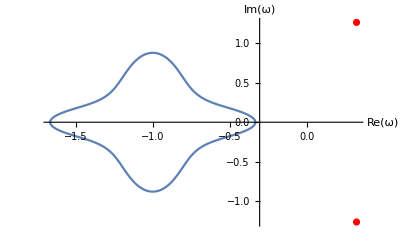

outlierx_example.csv

outliery_example.csv

```mathematica
(*Finding now the outlier eigenvalues...*)

(*Solving the simultaneous equations in Eq. (S82)*)
s = NSolve[{-(u + du + q^2 ddu) mychix + gammafracu complexity gammau mychix^2 + gammafracv complexity gammauv mychiy mychix ==-1,  -(u + dv + q^2 ddv) mychiy  + gammafracu complexity gammauv mychix mychiy + gammafracv complexity gammav mychiy^2  ==-1,  u1 == (1 + complexity u1) (gammafracu mychix*Conjugate[mychix] +gammafracv  mychiy*Conjugate[mychiy]), (gammafracu ncmuuu -1/mychix)(gammafracv ncmuvv -1/mychiy)-(gammafracv ncmuuv)( gammafracu ncmuvu) == 0},{mychix, mychiy, u, u1}];


eigx = {};
eigy = {};
(*Making sure the eigenvalues fit the criteria*)
For[k = 1, k<Length[s]+1, k++,
{chix, chiy, myu, myu1} = {mychix, mychiy, u, u1}/.s[[k]];
If[Re[myu1]>0,eigx = Append[eigx, Re[myu]];eigy = Append[eigy, Im[myu]];];
];

(*Plot the outliers alongside the boundary of the bulk and print values*)
plotpointsoutlier = Transpose[{eigx, eigy}];
outlierplot = ListPlot[plotpointsoutlier, PlotStyle->Red];
Show[lowerplot, upperplot, outlierplot, PlotRange->All, AxesLabel-> {ToExpression["\\mathrm{Re}[\\omega]",TeXForm,HoldForm],ToExpression["\\mathrm{Im}[\\omega]",TeXForm,HoldForm]}]

(*Export the results*)
Export["outlierx_example.csv",eigx]
Export["outliery_example.csv",eigy]
```